```mathematica
dmks2pi0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2](InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
dmkl3pi0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2]*(InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
dmklpipm0funct[m_,ep_]:=498/Sqrt[(m/2)^2-498^2]*(InterpolatingFunction[…][m/(2*498)*ep*(1+Sqrt[1-(2*498/m)^2])]-InterpolatingFunction[…][m/(2*498)*ep*(1-Sqrt[1-(2*498/m)^2])])
```

```mathematica
normfunc[dmm_,f_,ep_]:=NIntegrate[(f),{ep,0,dmm}]
```

```mathematica
dmks2pi0norma[dmm_,ep_]:=((4*0.307)/Quiet[normfunc[dmm,dmks2pi0funct[dmm,ep],ep]]*dmks2pi0funct[dmm,ep])
```

```mathematica
dmkl3pi0norma[dmm_,ep_]:=((0.195*6)/Quiet[normfunc[dmm,dmkl3pi0funct[dmm,ep],ep]]*dmkl3pi0funct[dmm,ep])
```

```mathematica
dmklpipm0norma[dmm_,ep_]:=((0.125*2)/Quiet[normfunc[dmm,dmklpipm0funct[dmm,ep],ep]]*dmklpipm0funct[dmm,ep])
```

```mathematica
kshortlong[m_,emax_]:=Quiet[Plot[{Evaluate[dmks2pi0norma[m,ep]],Evaluate[dmkl3pi0norma[m,ep]],Evaluate[dmklpipm0norma[m,ep]],Evaluate[dmks2pi0norma[m,ep]+dmkl3pi0norma[m,ep]+dmklpipm0norma[m,ep]]},{ep,0,emax},PlotRange->Full,PlotStyle->  {Red,Blue,Green,Black},PlotLegends->{"Ks -> 2π0","Kl -> 3π0","Kl -> π+π-π0","Total Ks Kl"},PlotLabel->m "MeV Dark Matter -> Ks Kl Photon Spectrum" ]]

kfile[m_,ep_] :=
Evaluate[dmks2pi0norma[1100,ep]+
dmkl3pi0norma[1100,ep]+
dmklpipm0norma[1100,ep]]

elist=Quiet[N@Subdivide[0.01,370,200]]
dataset={elist,kfile[1100, elist]}
SetDirectory@NotebookDirectory[]
Export["Kls PDFs\sdfg.csv",dataset, "CSV"]
```

{0.01,1.85995,3.7099,5.55985,7.4098,9.25975,11.1097,12.9597,14.8096,16.6596,18.5095,20.3595,22.2094,24.0594,25.9093,27.7593,29.6092,31.4592,33.3091,35.1591,37.009,38.859,40.7089,42.5589,44.4088,46.2588,48.1087,49.9587,51.8086,53.6586,55.5085,57.3585,59.2084,61.0584,62.9083,64.7583,66.6082,68.4582,70.3081,72.1581,74.008,75.858,77.7079,79.5579,81.4078,83.2578,85.1077,86.9577,88.8076,90.6575,92.5075,94.3575,96.2074,98.0574,99.9073,101.757,103.607,105.457,107.307,109.157,111.007,112.857,114.707,116.557,118.407,120.257,122.107,123.957,125.807,127.657,129.507,131.356,133.206,135.056,136.906,138.756,140.606,142.456,144.306,146.156,148.006,149.856,151.706,153.556,155.406,157.256,159.106,160.956,162.806,164.656,166.506,168.355,170.205,172.055,173.905,175.755,177.605,179.455,181.305,183.155,185.005,186.855,188.705,190.555,192.405,194.255,196.105,197.955,199.805,201.655,203.505,205.354,207.204,209.054,210.904,212.754,214.604,216.454,218.304,220.154,222.004,223.854,225.704,227.554,229.404,231.254,233.104,234.954,236.804,238.654,240.504,242.353,244.203,246.053,247.903,249.753,251.603,253.453,255.303,257.153,259.003,260.853,262.703,264.553,266.403,268.253,270.103,271.953,273.803,275.653,277.503,279.352,281.202,283.052,284.902,286.752,288.602,290.452,292.302,294.152,296.002,297.852,299.702,301.552,303.402,305.252,307.102,308.952,310.802,312.652,314.502,316.351,318.201,320.051,321.901,323.751,325.601,327.451,329.301,331.151,333.001,334.851,336.701,338.551,340.401,342.251,344.101,345.951,347.801,349.651,351.501,353.35,355.2,357.05,358.9,360.75,362.6,364.45,366.3,368.15,370.}

InterpolatingFunction::dmval: Input value {0.00635655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {201.09} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {202.266} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,1.85995,3.7099,5.55985,7.4098,9.25975,11.1097,12.9597,14.8096,16.6596,18.5095,20.3595,22.2094,24.0594,25.9093,27.7593,29.6092,31.4592,33.3091,35.1591,37.009,38.859,40.7089,42.5589,44.4088,46.2588,48.1087,49.9587,51.8086,53.6586,55.5085,57.3585,59.2084,61.0584,62.9083,64.7583,66.6082,68.4582,70.3081,72.1581,74.008,75.858,77.7079,79.5579,81.4078,83.2578,85.1077,86.9577,88.8076,90.6575,92.5075,94.3575,96.2074,98.0574,99.9073,101.757,103.607,105.457,107.307,109.157,111.007,112.857,114.707,116.557,118.407,120.257,122.107,123.957,125.807,127.657,129.507,131.356,133.206,135.056,136.906,138.756,140.606,142.456,144.306,146.156,148.006,149.856,151.706,153.556,155.406,157.256,159.106,160.956,162.806,164.656,166.506,168.355,170.205,172.055,173.905,175.755,177.605,179.455,181.305,183.155,185.005,186.855,188.705,190.555,192.405,194.255,196.105,197.955,199.805,201.655,203.505,205.354,207.204,209.054,210.904,212.754,214.604,216.454,218.304,220.154,222.004,223.854,225.704,227.554,229.404,231.254,233.104,234.954,236.804,238.654,240.504,242.353,244.203,246.053,247.903,249.753,251.603,253.453,255.303,257.153,259.003,260.853,262.703,264.553,266.403,268.253,270.103,271.953,273.803,275.653,277.503,279.352,281.202,283.052,284.902,286.752,288.602,290.452,292.302,294.152,296.002,297.852,299.702,301.552,303.402,305.252,307.102,308.952,310.802,312.652,314.502,316.351,318.201,320.051,321.901,323.751,325.601,327.451,329.301,331.151,333.001,334.851,336.701,338.551,340.401,342.251,344.101,345.951,347.801,349.651,351.501,353.35,355.2,357.05,358.9,360.75,362.6,364.45,366.3,368.15,370.},{0.,0.,0.,0.,0.,0.,0.,0.000167311,0.00100237,0.00173898,0.00242501,0.003241,0.00422897,0.0053527,0.0065712,0.00784973,0.00916056,0.0104358,0.0113936,0.0123516,0.0132982,0.0142242,0.0151231,0.0159901,0.0168148,0.0175755,0.0182592,0.0188638,0.0193903,0.0198419,0.0202224,0.020536,0.020787,0.0209798,0.0211185,0.021207,0.0212492,0.0212486,0.0212086,0.0211324,0.0210229,0.0208831,0.0207154,0.0205224,0.0203064,0.0200696,0.019814,0.0195417,0.0192545,0.0189542,0.0186424,0.018321,0.0179916,0.0176558,0.0173152,0.0169717,0.0166271,0.0162835,0.0159437,0.01561,0.0152824,0.0149611,0.0146462,0.0143378,0.0140359,0.0137405,0.0134518,0.0131696,0.0128941,0.0126251,0.0123627,0.0121069,0.0118575,0.0116146,0.011378,0.0111478,0.0109238,0.010706,0.0104942,0.0102673,0.00998886,0.00971725,0.00945237,0.0091941,0.00894233,0.00869696,0.00845786,0.00822493,0.00799805,0.00777711,0.007562,0.00735261,0.00714883,0.00695056,0.00675767,0.00657007,0.00638766,0.00621032,0.00603796,0.00587047,0.00570775,0.0055497,0.00539623,0.00524724,0.00510263,0.0049623,0.00482618,0.00469415,0.00456614,0.00444204,0.00432178,0.00420527,0.00409241,0.00398312,0.00387731,0.00377491,0.00367582,0.00357996,0.00348725,0.0033976,0.00331093,0.00322716,0.0031462,0.00306797,0.00299239,0.00291937,0.00284882,0.00278066,0.0027148,0.00265116,0.00258964,0.00253016,0.00247261,0.00241691,0.00236295,0.00231064,0.00225986,0.0022105,0.00216244,0.00211554,0.00206968,0.00202471,0.0019804,0.00193649,0.00189288,0.00184957,0.00180656,0.00176385,0.00172142,0.00167928,0.00163742,0.00159584,0.00155453,0.0015135,0.00147273,0.00143222,0.00139198,0.00135199,0.00131226,0.00127278,0.00123354,0.00119455,0.0011558,0.00111729,0.00107902,0.00104098,0.00100316,0.000965578,0.000928217,0.000891078,0.000854158,0.000817454,0.000780965,0.000744686,0.000708617,0.000672755,0.000637097,0.000601641,0.000566385,0.000531326,0.000496463,0.000461793,0.000427313,0.000393023,0.000358919,0.000325001,0.000291265,0.00025771,0.000224334,0.000191135,0.000158112,0.000125261,0.0000925826,0.0000600735,0.0000277325,0.,0.,0.,0.,0.,0.}}

C:\Users\jacob\Desktop\EtaPion

Kls PDFs\sdfg.csv

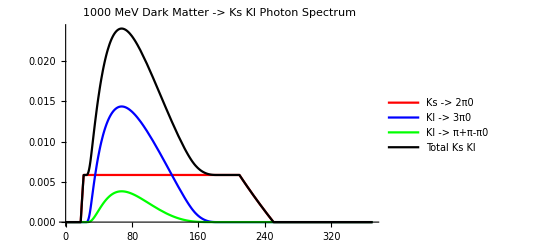

```mathematica
kshortlong[1000,370]
```

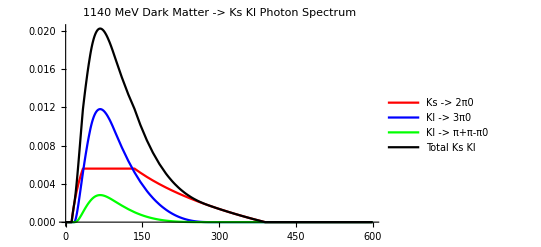

```mathematica
kshortlong[1140,600]
```

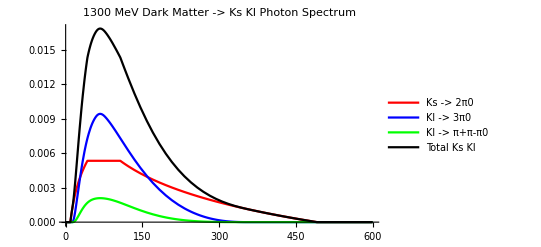

```mathematica
kshortlong[1300,600]
```

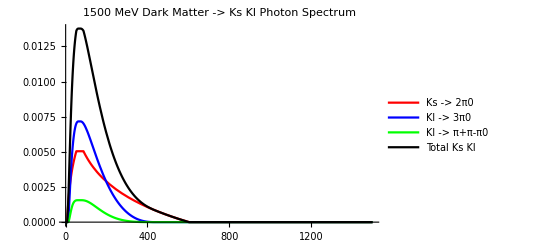

```mathematica
kshortlong[1500,1500]
```

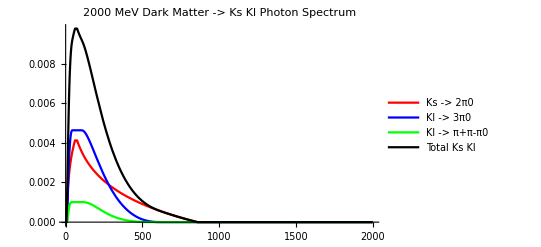

```mathematica
kshortlong[2000,2000]
```

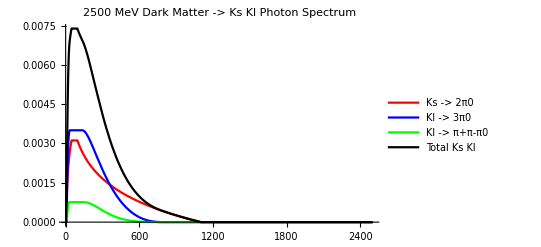

```mathematica
kshortlong[2500,2500]
```

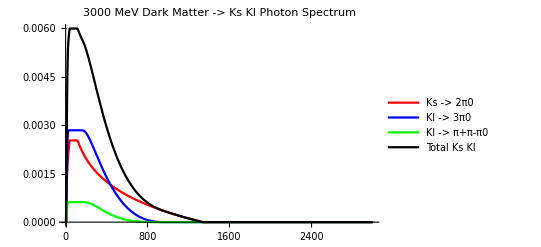

```mathematica
kshortlong[3000,3000]
```

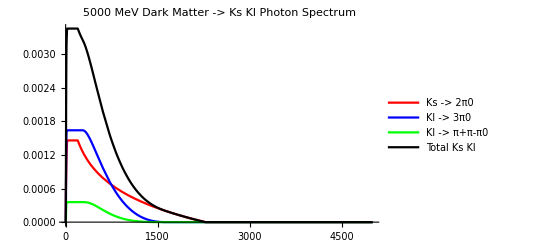

```mathematica
kshortlong[5000,5000]
```

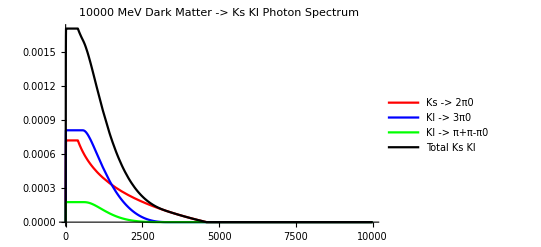

```mathematica
kshortlong[10000,10000]
```

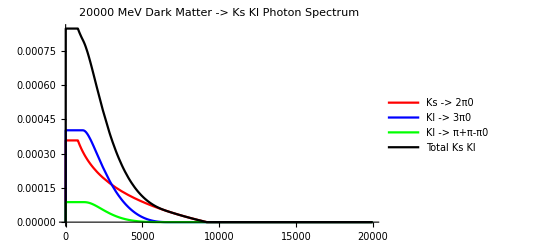

```mathematica
kshortlong[20000,20000]
```

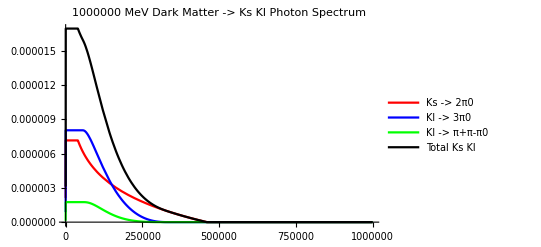

```mathematica
kshortlong[1000000,1000000]
```

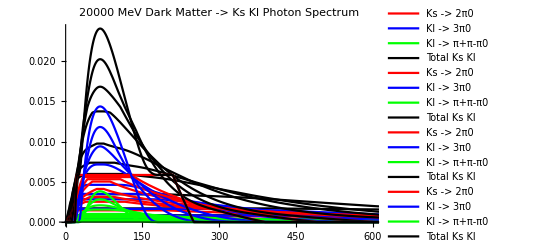

```mathematica
Show[Out[82],Out[81],Out[80],Out[79],Out[78],Out[64],Out[77],Out[76],Out[75],Out[74],PlotRange-> {{0,600},Full}]
```

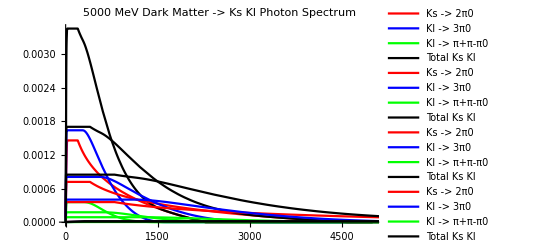

```mathematica
Show[Out[80],Out[81],Out[82],Out[98]]
```

```mathematica
justtotal[m_]:=Quiet[Plot[Evaluate[dmks2pi0norma[m,ep]+dmkl3pi0norma[m,ep]+dmklpipm0norma[m,ep]],{ep,0,m},PlotRange->Full,PlotLegends-> {m "MeV"},PlotStyle->RandomColor[]]]
```

```mathematica
totalspread[mlist_,x_]:=Show[(justtotal[#])&/@mlist,PlotRange-> {{0,x},Full}]
```

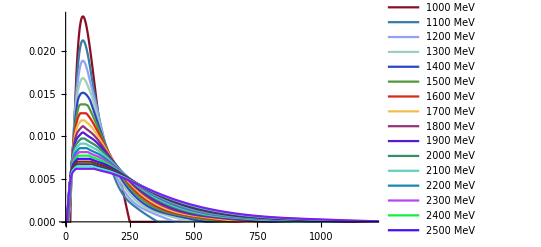

```mathematica
totalspread[Table[1000+100*(i-1),{i,20}],1200]
```

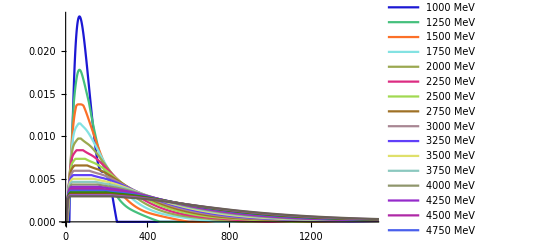

```mathematica
totalspread[Table[1000+250*(i-1),{i,20}],1500]
```

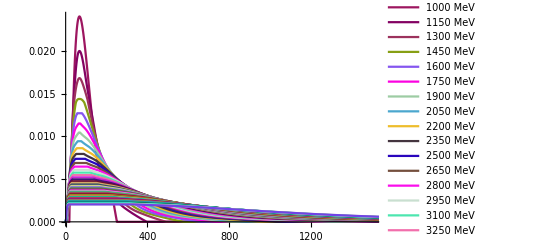

```mathematica
totalspread[Table[1000+150*(i-1),{i,50}],1500]
```

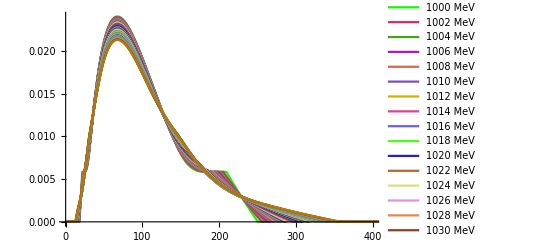

```mathematica
totalspread[Table[1000+2*(i-1),{i,50}],400]
```

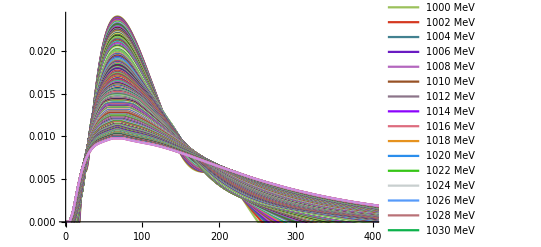

```mathematica
totalspread[Table[1000+2*(i-1),{i,500}],400]
```

```mathematica
Show[{Out[198],Out[199],Out[201],Out[207],Out[209]},PlotRange-> {{0,400},Full}]
```

-Graphics-